# GRAVITAS Figure Reproductions

Luke Wriglesworth

Wolfram Institute

Here I reproduce some of the key results from Jonathan Gorard’s GRAVITAS papers, which provide a framework for working with General Relativity in the Wolfram Physics Project.

## Computational General Relativity in the Wolfram Language using Gravitas II: ADM Formalism and Numerical Relativity

https://arxiv.org/abs/2401.14209

### Figure 49, pg. 61

“A DiscreteHypersurfaceDecomposition object for a Schwarzschild geometry (representing, for instance, an uncharged, non-rotating black hole with numerical mass 1 in Schwarzschild or spherical polar coordinates (t, r, θ, ϕ) with t ∈ [0, 1], r ∈ [0, 4] and θ ∈ [−π, π]), with a resolution of 400 vertices and a discretization scale of 1.2, represented by the evolution of its spatial hypergraphs for five time steps from coordinate time t = 0 to coordinate time t = 1 (colored based on extrinsic curvature) with spatial coordinate information assigned to the vertices.”

```mathematica
schwarzschildTensor = MetricTensor[{"Schwarzschild",1},{t,r,θ,ϕ}];
decomposition = DiscreteHypersurfaceDecomposition[schwarzschildTensor,{t,0,1},{r,0,4},{θ,-Pi,Pi},400,1.2];
schwarzschildTensor["MatrixRepresentation"]//MatrixForm
decomposition[{"CoordinatizedPolarGraphEvolutionColored",5}]
```

(-1+2/r | 0 | 0 | 0
0 | 1/(1-2/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

“ A DiscreteHypersurfaceDecomposition object for a Kerr geometry (representing, for instance, an uncharged, spinning black hole with numerical mass 1 and numerical angular momentum 1/3 in Boyer-Lindquist or oblate spheroidal coordinates (t, r, θ, ϕ) with t ∈ [0, 1], r ∈ [0, 4] and θ ∈ [−π, π]), with a resolution of 400 vertices and a discretization scale of 1.2, represented by the evolution of its spatial hypergraphs for five time steps from coordinate time t = 0 to coordinate time t = 1 (colored based on extrinsic curvature) with spatial coordinate information assigned to
the vertices.”

```mathematica
kerrTensor = MetricTensor[{"Kerr",1,1/3},{t,r,θ,ϕ}];
decomposition = DiscreteHypersurfaceDecomposition[kerrTensor,{t,0,1},{r,0,4},{θ,-Pi,Pi},400,1.2];
kerrTensor["MatrixRepresentation"]//MatrixForm
decomposition[{"CoordinatizedPolarGraphEvolutionColored",5}]
```

(-1+(2 r)/(r^2+Cos[θ]^2/9) | 0 | 0 | -(2 r Sin[θ]^2)/(3 (r^2+Cos[θ]^2/9))
0 | (r^2+Cos[θ]^2/9)/(1/9-2 r+r^2) | 0 | 0
0 | 0 | r^2+Cos[θ]^2/9 | 0
-(2 r Sin[θ]^2)/(3 (r^2+Cos[θ]^2/9)) | 0 | 0 | Sin[θ]^2 (1/9+r^2+(2 r Sin[θ]^2)/(9 (r^2+Cos[θ]^2/9))))

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Figure 50, pg. 62

“A DiscreteHypersurfaceDecomposition object for a Schwarzschild geometry (representing, for instance, an uncharged, non-rotating black hole with numerical mass 1 in Schwarzschild or spherical polar coordinates (t, r, θ, ϕ) with t ∈ [0, 1], r ∈ [0, 4] and θ ∈ [−π, π]), with a resolution of 400 vertices and a discretization scale of 1.2, represented by the evolution of its spatial hypergraphs for five time steps from coordinate time t = 0 to coordinate time t = 1 (colored based on extrinsic curvature) without any vertex coordinate information assigned.”

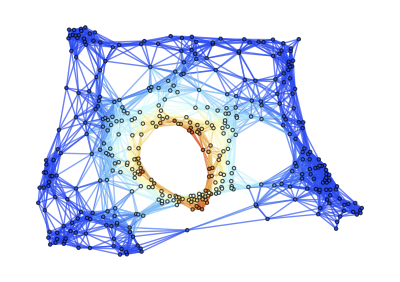
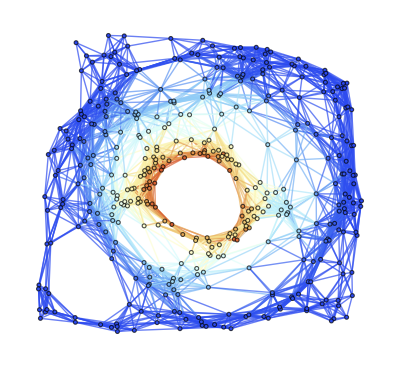
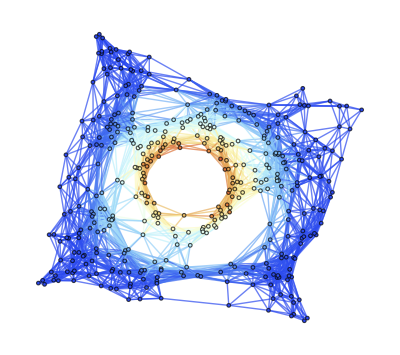
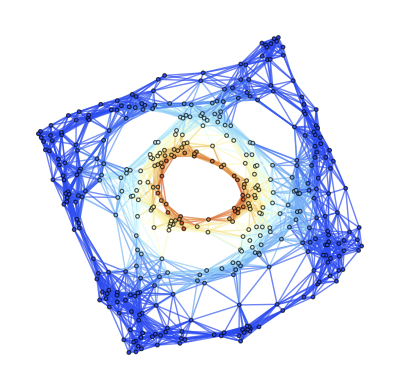
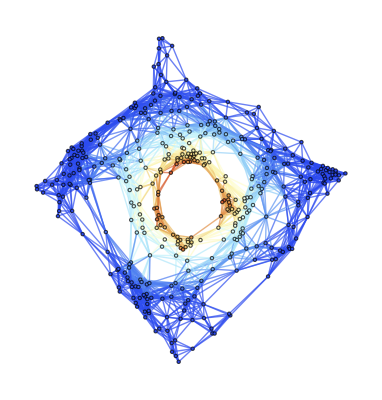
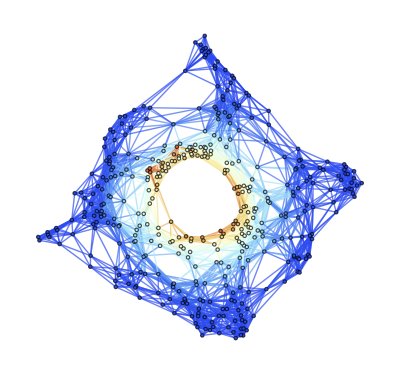

```mathematica
schwarzschildTensor = MetricTensor[{"Schwarzschild",1},{t,r,θ,ϕ}];
decomposition = DiscreteHypersurfaceDecomposition[schwarzschildTensor,{t,0,1},{r,0,4},{θ,-Pi,Pi},400,1.2];
decomposition[{"PolarGraphEvolutionColored",5}]
```

“A DiscreteHypersurfaceDecomposition object for a Kerr geometry (representing, for instance, an uncharged, spinning black hole with numerical mass 1 and numerical angular momentum 1/3 in Boyer-Lindquist or oblate spheroidal coordinates (t, r, θ, ϕ) with t ∈ [0, 1], r ∈ [0, 4] and θ ∈ [−π, π]), with a resolution of 400 vertices and a discretization scale of 1.2, represented by the evolution of its spatial hypergraphs for five time steps from coordinate time t = 0 to coordinate time t = 1 (colored based on extrinsic curvature) without any vertex coordinate information assigned.”

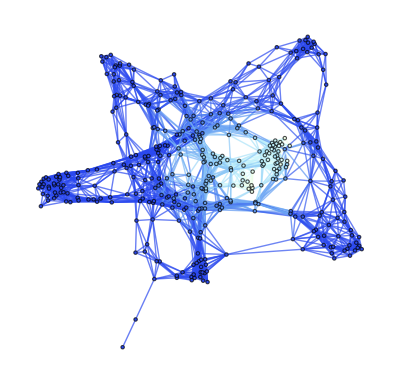
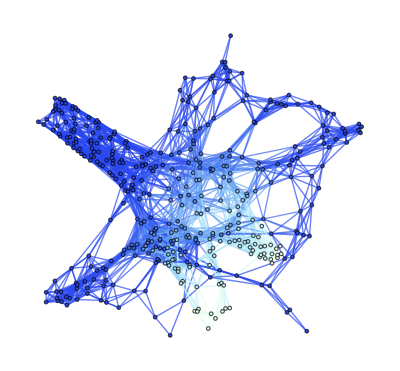
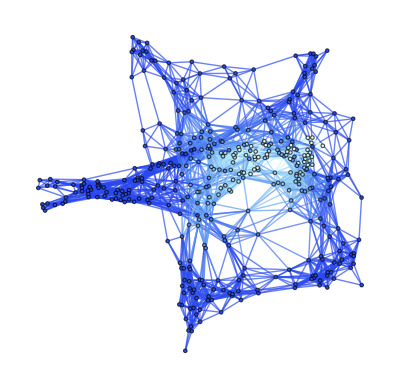
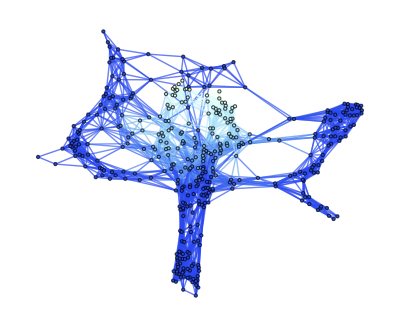
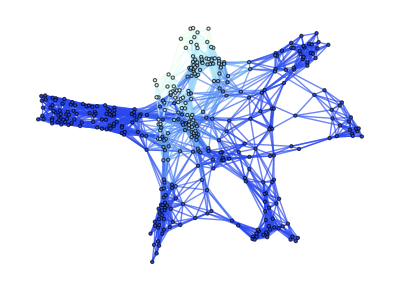
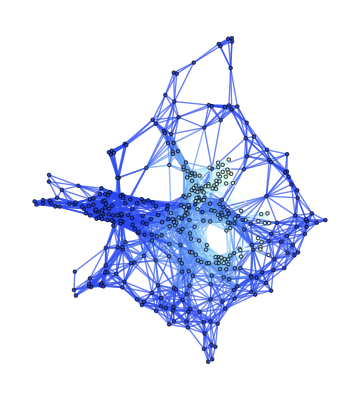

```mathematica
schwarzschildTensor = MetricTensor[{"Kerr",1,1/3},{t,r,θ,ϕ}];
decomposition = DiscreteHypersurfaceDecomposition[schwarzschildTensor,{t,0,1},{r,0,4},{θ,-Pi,Pi},400,1.2];
decomposition[{"PolarGraphEvolutionColored",5}]
```

## Figure 52, pg. 65

“The DiscreteHypersurfaceDecomposition object for a Brill-Lindquist geometry (representing, for instance, a pair of uncharged, non-rotating black holes, initially at rest, each of mass M in Schwarzschild or spherical polar coordinates (t, r, θ, ϕ) with the radial boundary R of the domain set to be comparable to the Schwarzschild radii of the black holes, i.e. R ∼ 2M ) with the 1 + log slicing condition and the minimal distortion coordinate conditions for the gauge, represented by the evolution of its spatial hypergraphs for six time steps from coordinate time t = 0M to coordinate time t = 24M (colored based on extrinsic curvature) without any vertex coordinate information assigned.”

```mathematica
adm=ADMDecomposition[{"BrillLindquist",1,1},t,{r,θ,ϕ},1,{0,0,0}];
tensor = adm["SpacetimeMetricTensor"]
decomposition = DiscreteHypersurfaceDecomposition[tensor,{t,0,1},{r,0,1},{θ,-Pi,Pi},10,1.2]
decomposition[{"PolarGraphEvolutionColored",5}]
```

MetricTensor[…]

DiscreteHypersurfaceDecomposition[…]

$Aborted

```mathematica
Needs["PacletTools`"];
PacletBuild["/home/luke/Code/Gravitas"];
PacletInstall["/home/luke/Code/Gravitas/build/Gravitas-1.0.0.paclet", ForceVersionInstall->True];
Needs["Gravitas`"]
```